```mathematica
ListPlot[{4,3,2,1,1,1,1,1,2,3,4}]
```

-Graphics-

```mathematica
ListPlot[{{0.1,4},{0.2,3},{0.3,2},{0.4,1},{0.9,1},{1.0,1},{1.1,1},{1.2,2},{1.6,3},{1.7,4}}]
```

-Graphics-



```mathematica
Graphics[Circle[]]
```

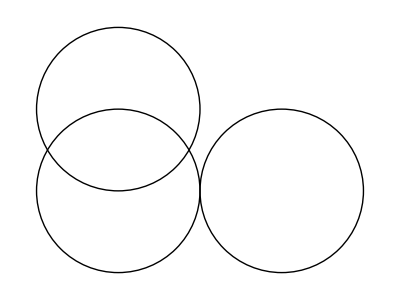

```mathematica
Graphics[{Circle[{1,1}],Circle[{1,2}],Circle[{3,1}]}]
```

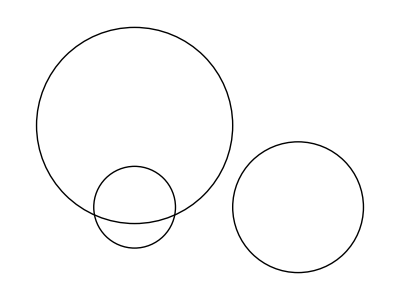

```mathematica
Graphics[{Circle[{1,1},0.5],Circle[{1,2},1.2],Circle[{3,1},0.8]}]
```

```mathematica
Rasterize[Graphics[{Circle[{1,1},0.5],Circle[{1,2},1.2],Circle[{3,1},0.8]}],"Image"]
```

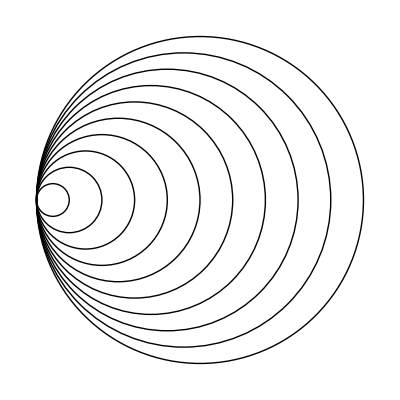

```mathematica
Graphics[Table[Circle[{x,0},x],{x,1,10}]]
```

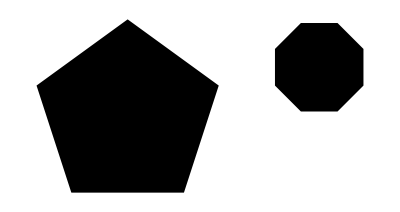

```mathematica
Graphics[{RegularPolygon[{1,3},2,5],RegularPolygon[{5,4},1,8]}]
```

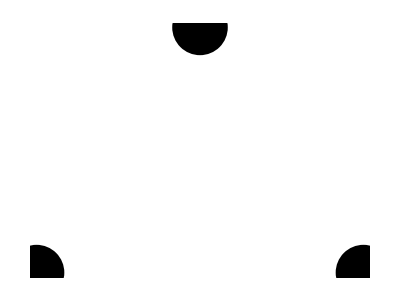

```mathematica
Graphics[{PointSize[0.1],Point[{0,0}],Point[{2,0}],Point[{1,1.5}]}]
```

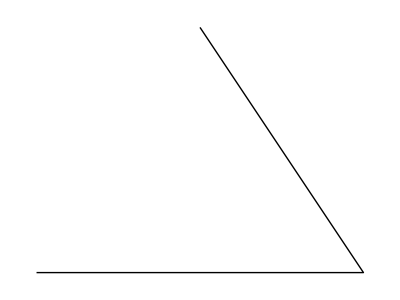

```mathematica
Graphics[Line[{{0,0},{2,0},{1,1.5}}]]
```

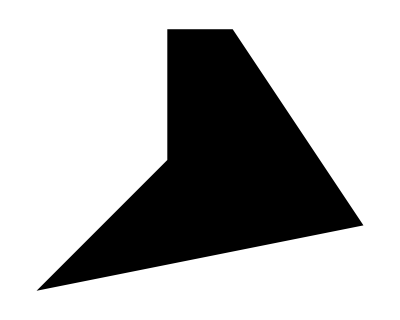

```mathematica
Graphics[Polygon[{{0,0},{5,1},{3,4},{2,4},{2,2}}]]
```

```mathematica
Graphics3D[{Sphere[{0,0,0},2],Sphere[{0,0,3},1]}]
```

-Graphics3D-

```mathematica
Graphics3D[Table[Point[{x,y,z}],{x,0,6},{y,0,6},{z,0,6}]]
```

-Graphics3D-

```mathematica
Graphics3D[{Table[Point[{x,y,z}],{x,0,6},{y,0,6},{z,0,6}],Sphere[{1,3,3},0.5],Sphere[{3,3,3},1.2]}]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[{Table[Point[{x,y,z}],{x,0,6},{y,0,6},{z,0,6}],Sphere[{x,3,3},0.5],Style[Sphere[{3,3,3},1.2],Opacity[o]]}], {x,1,5},{o,0,1}]
```

Vocabulary
	skip